```mathematica
NS["study_overlearning6"]
```

```mathematica
label="sd100o2_75_5000.csv";scores=Flatten@Import["avgscores_"<>label];
lh1=T@Import["avglh1_"<>label];lh2=T@Import["avglh2_"<>label];
lev=Flatten@Import["avglogev_"<>label];
pro=Import["avgprobs_"<>label];
surpr=Flatten@Import["avgsurprise_"<>label];

sdscores=Flatten@Import["sdscores_"<>label];
sdlh1=T@Import["sdlh1_"<>label];sdlh2=T@Import["sdlh2_"<>label];
sdlev=Flatten@Import["sdlogev_"<>label];
sdpro=Import["sdprobs_"<>label];
sdsurpr=Flatten@Import["sdsurprise_"<>label];
ffreqs=(#/Total/@#)&@Import["avgfreqs_"<>label];sdffreqs=(#/Total/@#)&@Import["sdfreqs_"<>label];
(*ffreqs=(#/Total/@#)&@Import["finalfreqs_"<>label];*)
ofreqs=T@Import["targetfreqs_"<>label];
nsamples=Length@scores
```

75

```mathematica
nn=Sqrt[5000];
```

```mathematica
ofreqs
```

{{0.0454545,0.0454545,0.909091},{0.409091,0.409091,0.181818}}

```mathematica
ffreqs//N
```

{{0.0460306,0.0458067,0.908163},{0.40784,0.411857,0.180303}}

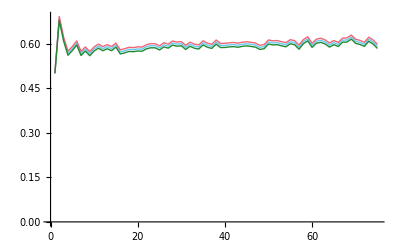

```mathematica
ListPlot[{scores,scores+sdscores/nn,scores-sdscores/nn},Joined->True,PlotRange->{All,{0,All}}]
```

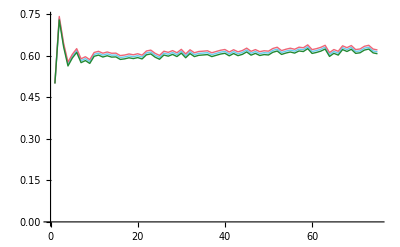

```mathematica
Exp@-surpr
```

{0.5,0.310329,0.250506,0.256424,0.289286,0.313509,0.349393,0.368543,0.397542,0.42123,0.428649,0.447064,0.450261,0.457672,0.469396,0.468483,0.474661,0.475809,0.481127,0.481818,0.481592,0.487835,0.490182,0.484985,0.489691,0.487943,0.490137,0.490332,0.491499,0.490535,0.490003,0.492547,0.492761,0.492263,0.493675,0.492529,0.490674,0.492474,0.492358,0.493169,0.492224,0.4948,0.491085,0.49283,0.496089,0.49373,0.493918,0.493488,0.493172,0.494899,0.495184,0.496336,0.495038,0.49405,0.495943,0.495261,0.496398,0.496173,0.497686,0.495819,0.495238,0.496944,0.49684,0.495146,0.496596,0.494045,0.496194,0.496132,0.497994,0.496185,0.49653,0.496414,0.496832,0.495677,0.494739}

```mathematica
GeometricMean[{0.4,0.5,0.5,0.6}]
```

0.494923

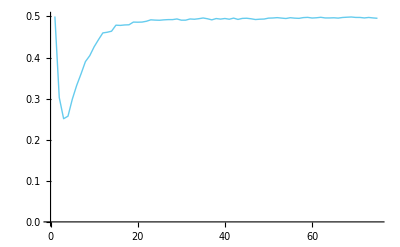

```mathematica
ListPlot[Exp@-surpr,GridLines->None,Joined->True,PlotRange->{0,All}]
```

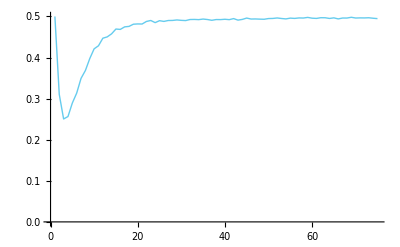

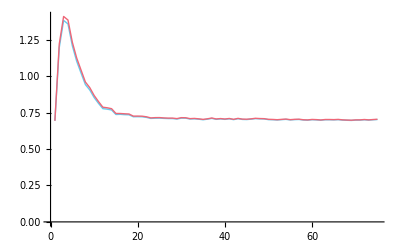

```mathematica
ListPlot[{surpr,surpr+sdsurpr/nn},GridLines->None,Joined->True,PlotRange->{0,All}]
```

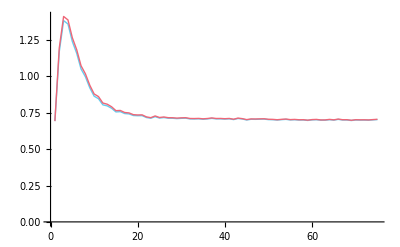

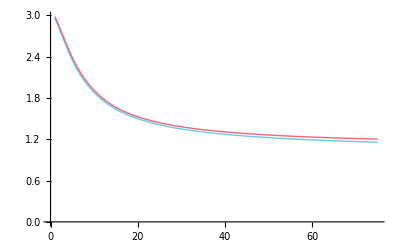

```mathematica
ListPlot[{-lev/Range@Length@lev,-lev/Range@Length@lev+sdlev/nn},Joined->True,PlotRange->All]
```

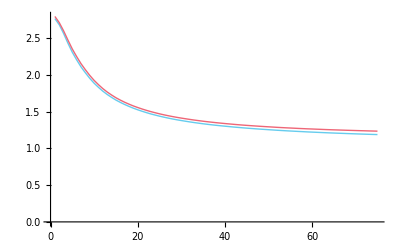

```mathematica
(* define a parametric family for a 3-outcome space *)
```

```mathematica
expsum[t_]=Table[(1+KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=FullSimplify[expsum[t]/z[t]]
```

{1/((1+ⅇ^t)^2),ⅇ^(2 t)/((1+ⅇ^t)^2),1/(1+Cosh[t])}

```mathematica
(* coords transfs to plot the two-distribution space *)
```

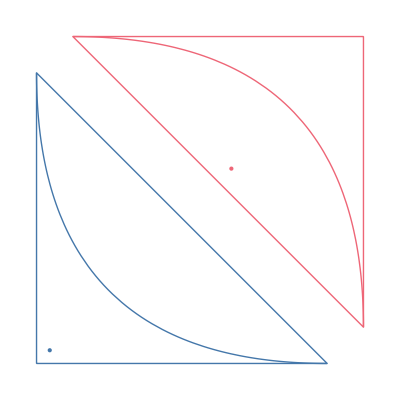

```mathematica
offset=9/8;
c1[p_]:=p[[{1,2}]];
c2[p_]:=offset-p[[{2,1}]];
plotfreqs[freqs_]:=Block[{nfreqs=(#/Total@T@#)&@freqs},Graphics[{{PointSize@Large,purpleblue,Point[c1@nfreqs[[1]]]},{PointSize@Large,red,Point[c2@nfreqs[[2]]]}}]];
plotcfreqs[freqs_]:=Block[{nfreqs=(#/Total@T@#)&@freqs},Graphics[{{Thick,purpleblue,Circle[c1@nfreqs[[1]],0.02]},{Thick,red,Circle[c2@nfreqs[[2]],0.02]}}]];
sp1={purpleblue,Thin,Line[{{0,0},{1,0},{0,1},{0,0}}]};
sp2={red,Thin,Line[offset-{{0,0},{1,0},{0,1},{0,0}}]};
pplot1=ParametricPlot[c1@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];
pplot2=ParametricPlot[c2@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,red}];
doms={Graphics[{sp1,sp2}],pplot1,pplot2};
Show[{doms,plotfreqs[ofreqs]},PlotRange->All]
```

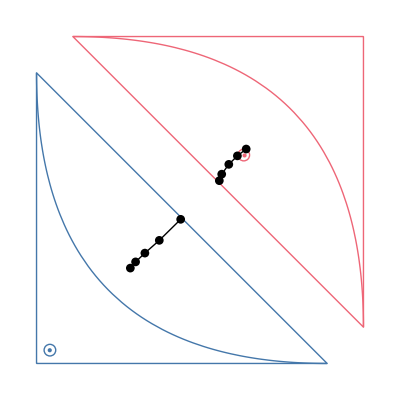

```mathematica
subrange=Round[Range[1,5,nsamples/nsamples]];rplot1=ListPlot[Table[c1@lh1[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];rplot2=ListPlot[Table[c2@lh2[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{doms,plotfreqs@ofreqs,plotcfreqs@ffreqs,rplot1,rplot2},PlotRange->All]
```

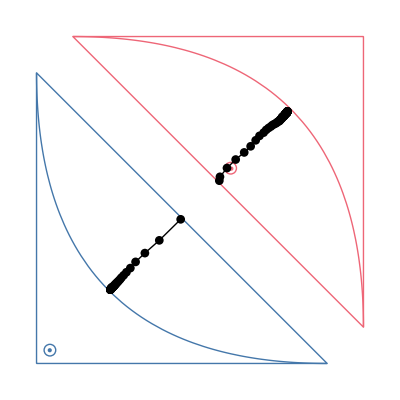

-Graphics-

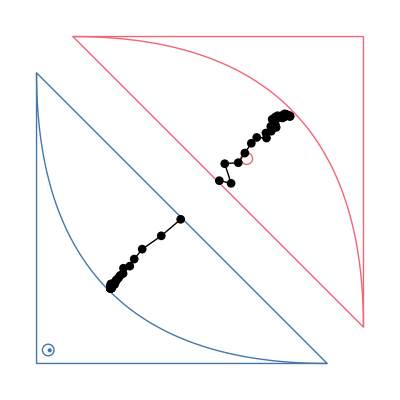

-Graphics-

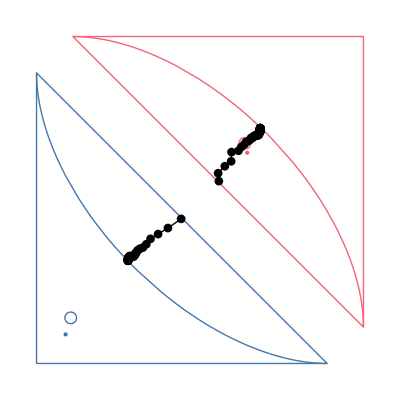

-Graphics-

```mathematica
(* algorithm to predict & update from data *)
```

```mathematica
hi={1/2,1/2};
prior[t_,m_,s_]=PDF[NormalDistribution[m,s],t];
```

```mathematica
(* generate data *)
```

```mathematica
SeedRandom[998];
ofreqs={{6,3,1},{3,6,1}}/10;
```

```mathematica
data=T@Import["baddata.csv"]
```

{{1,3},{2,1},{1,3},{1,3},{2,1},{2,2},{2,2},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{2,1},{2,3},{2,2},{2,1},{1,3},{1,3},{2,1},{1,3},{1,3},{1,3},{1,3},{1,3},{2,1},{2,3},{1,3},{1,3},{2,1},{1,3},{2,2},{2,2},{1,3},{1,3},{1,3},{2,1},{1,3},{1,3},{2,2},{1,3},{1,3},{1,3},{1,3},{2,2},{2,2},{1,3},{2,1},{2,2},{2,2}}

```mathematica
Tally[data]
```

{{{1,3},29},{{2,1},9},{{2,2},10},{{2,3},2}}

```mathematica
nsamples=100;
data=Table[{h=RandomSample[hi->Range[2],1][[1]],RandomSample[ofreqs[[h]]->Range[3],1][[1]]},{nsamples}];
```

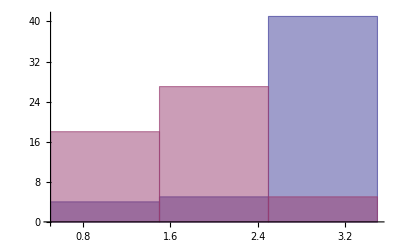

```mathematica
Histogram[Table[Pick[data[[;;,2]],data[[;;,1]],i],{i,2}]]
```

```mathematica
ProgressIndicator[Dynamic[i],{0,nsamples}]
```

```mathematica
nsamples=Length[data];m=0;s=100;freqs=Table[0,{2},{3}];evidence=Table[1,{2}];
likelihood=Table[Null,{nsamples}];probh=likelihood;
logev=Table[Null,{nsamples}];

Do[
integral=Table[
NIntegrate[prob[t]*Times@@(prob[t]^freqs[[j]])*prior[t,m,s],{t,-Infinity,+Infinity}],{j,2}];
Print[{i,integral//MF}];
likelihood[[i]]=Table[
integral[[j]]/evidence[[j]],{j,2}];

probh[[i]]=(#/Total[#])&@(likelihood[[i,;;,data[[i,2]]]]*hi);

evidence[[data[[i,1]]]]=integral[[data[[i,1]],data[[i,2]]]];
logev[[i]]=Total@Log[evidence];
++freqs[[data[[i,1]],data[[i,2]]]];
,{i,nsamples}]
```

```mathematica
Dimensions[logev]
```

{100}

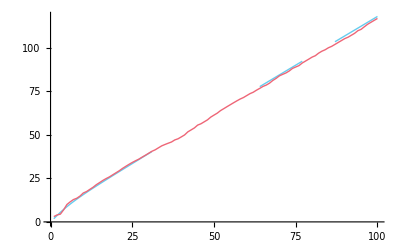

```mathematica
ListPlot[{-Flatten@lev,-logev},Joined->True,PlotRange->All]
```

```mathematica
Log[evidence]//MF
```

(-57.8741
-56.1967)

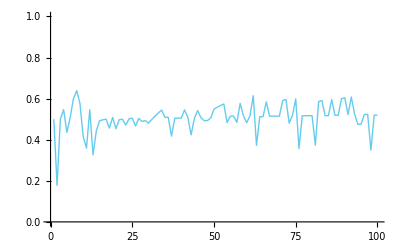

```mathematica
ListPlot[Table[probh[[i,data[[i,1]]]],{i,nsamples}],Joined->True,PlotRange->{0,1}]
```

```mathematica
subrange=Round[Range[1,nsamples,nsamples/nsamples]];
```

```mathematica
rplot1=ListPlot[Table[c1@likelihood[[i,1]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];rplot2=ListPlot[Table[c2@likelihood[[i,2]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
```

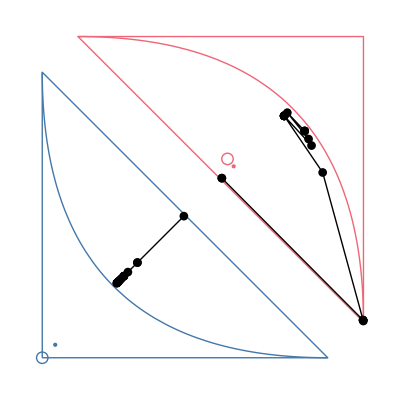

```mathematica
Show[{doms,plotfreqs@ofreqs,plotcfreqs@freqs,rplot1,rplot2},PlotRange->All]
```

```mathematica
nobs=15;data=RandomChoice[freq->{1,2,3},nobs];
```

```mathematica
nsamples=25;
updens[0]=FS[(m-1)^4/Integrate[(m-1)^4,{m,0,2}]];
upprob[0]=FS@NIntegrate[probm*updens[0],{m,0,2}];
```

```mathematica
Do[
datas=RandomSample[data];
updens[sample,0]=updens[0];
upprob[sample,0]=upprob[0];
Do[Print[sample," -",i];updens[sample,i]=Assuming[0<m<2,FS[probm[[datas[[i]]]]*updens[sample,i-1]/NIntegrate[probm[[datas[[i]]]]*updens[sample,i-1],{m,0,2}]]];
upprob[sample,i]=FS@NIntegrate[probm*updens[sample,i],{m,0,2}],{i,1,nobs}];,{sample,1,nsamples}];
```

```mathematica
Do[upprob[i]=Mean[Table[upprob[sample,i],{sample,nsamples}]],{i,nobs}];{upprob[nobs],freq}//N//MF
```

(0.107483 | 0.252758 | 0.639759
0.2 | 0.2 | 0.6)

```mathematica
Table[upprob[samples,nobs],{samples,8}]//MF
```

(0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759)

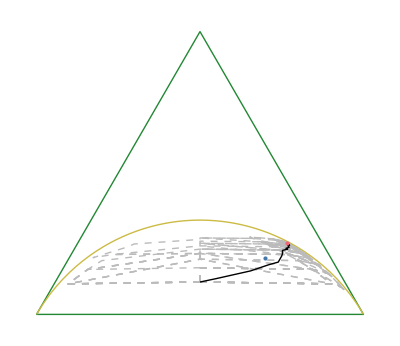

```mathematica
Show[Join[{triangle,parplot,Graphics[{purpleblue,PointSize[Medium],Point[finpoints.freq]}]},
Table[Graphics[{Dashed,Thin,grey,Line[T[finpoints.T[Table[upprob[sample,i],{i,0,nobs}]]]]}],{sample,nsamples}],{
Graphics@Line[T[finpoints.T[Table[upprob[i],{i,0,nobs}]]]],Graphics[{red,PointSize[Medium],Point[finpoints.upprob[nobs]]}]}]]
```

```mathematica
expdf0["overlearning1"]
```

overlearning1.pdf

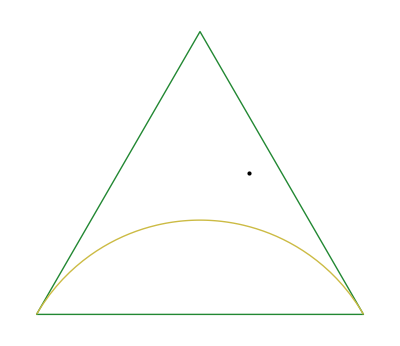

```mathematica
freq2={1/10,1-5/10,4/10};Show[{triangle,parplot,Graphics@Point[finpoints.freq2]}]
```

```mathematica
nobs2=15;data2=RandomChoice[freq2->{1,2,3},nobs2];
```

```mathematica
nsamples2=25;
updens2[0]=FS[(m-1)^4/Integrate[(m-1)^4,{m,0,2}]];
upprob2[0]=FS@NIntegrate[probm*updens2[0],{m,0,2}];
```

```mathematica
Do[
datas=RandomSample[data2];
updens2[sample,0]=updens2[0];
upprob2[sample,0]=upprob2[0];
Do[Print[sample," -",i];updens2[sample,i]=Assuming[0<m<2,FS[probm[[datas[[i]]]]*updens2[sample,i-1]/NIntegrate[probm[[datas[[i]]]]*updens2[sample,i-1],{m,0,2}]]];
upprob2[sample,i]=FS@NIntegrate[probm*updens2[sample,i],{m,0,2}],{i,1,nobs2}];,{sample,1,nsamples2}];
```

```mathematica
Do[upprob2[i]=Mean[Table[upprob2[sample,i],{sample,nsamples2}]],{i,nobs2}];{upprob2[nobs2],freq2}//N//MF
```

(0.13709 | 0.271276 | 0.591634
0.1 | 0.5 | 0.4)

```mathematica
Table[upprob2[samples,nobs2],{samples,8}]//MF
```

(0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634)

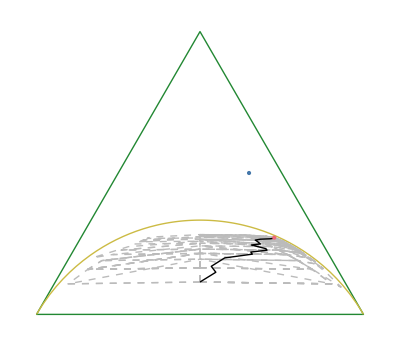

```mathematica
Show[Join[{triangle,parplot,Graphics[{purpleblue,PointSize[Medium],Point[finpoints.freq2]}]},
Table[Graphics[{Dashed,Thin,grey,Line[T[finpoints.T[Table[upprob2[sample,i],{i,0,nobs2}]]]]}],{sample,nsamples2}],{
Graphics@Line[T[finpoints.T[Table[upprob2[i],{i,0,nobs2}]]]],Graphics[{red,PointSize[Medium],Point[finpoints.upprob2[nobs2]]}]}]]
```

```mathematica
expdf0["overlearning2"]
```

overlearning2.pdf